```mathematica
numbers={a->1.,ν->0.07453,α->0.000002};
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\Загрузки\Диплом\Diploma_Nb

```mathematica
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogLinearPlot},PlotRange->Full,Axes->False,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Courier",FontSize->12, Bold},ImageSize->500,PlotStyle->{Red,PointSize[0.01]}];
```

```mathematica
AbsFourier[x_]:=Abs[Take[Fourier[x,FourierParameters->{-1, -1}],{1,Length[x]/2+1}]]
```

```mathematica
NumPlace[x_]:=Position[AbsFourier[x],Max[AbsFourier[x]]][[1,1]]
```

```mathematica
FreqList[x_]:=Table[1.0*b/Length[x],{b,0,Length[x]-1}]
```

```mathematica
Freq[x_]:=FreqList[x][[NumPlace[x]]]
```

```mathematica
TruePlot[x_]:=ListPlot[Transpose[{FreqList[x][[1;;NumPlace[x]+4]],AbsFourier[x][[1;;NumPlace[x]+4]]}],FrameLabel->{"ν","A, mm"}]
FullPlot[x_]:=ListPlot[Transpose[{FreqList[x][[1;;Length[x]/2+1]],AbsFourier[x]}],FrameLabel->{"ν","A, mm"}]
NuGass[x_]:=Freq[x]+(AbsFourier[x][[NumPlace[x]+1]]-AbsFourier[x][[NumPlace[x]-1]])/(2*(2*AbsFourier[x][[NumPlace[x]]]-AbsFourier[x][[NumPlace[x]+1]]-AbsFourier[x][[NumPlace[x]-1]]))/Length[x]
```

0% Level

```mathematica
sig0=Table[a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,500}];
```

0.074

0.0741372

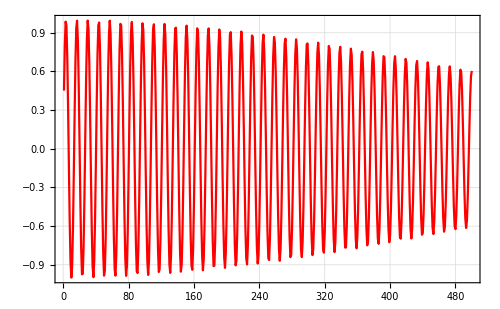

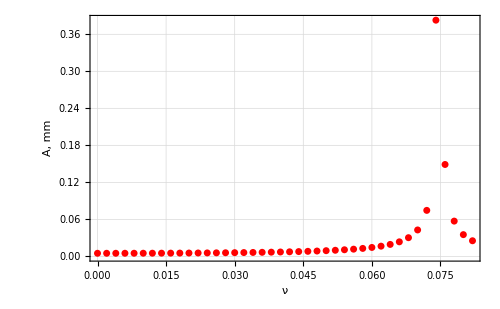

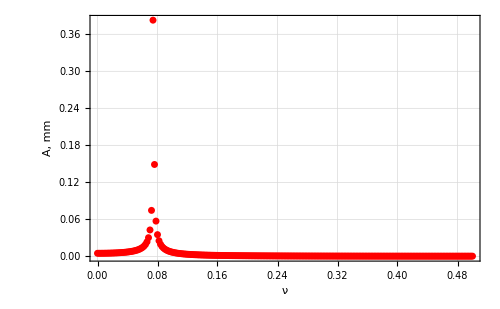

```mathematica
Freq0 =Freq[sig0]
NuGass0=NuGass[sig0]
Image0=ListLinePlot[sig0]
Fourier0=TruePlot[sig0]
FourierFull0=FullPlot[sig0]
```

25% Level

```mathematica
sig25=Table[0.5*(Random[]-0.5)+a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,500}];
```

0.074

0.0741533

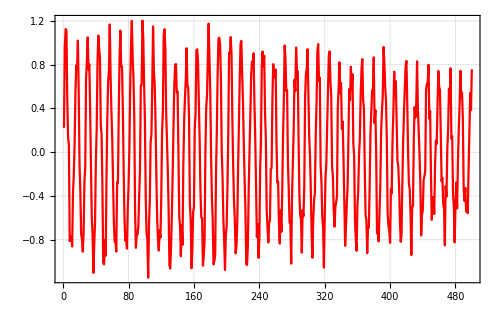

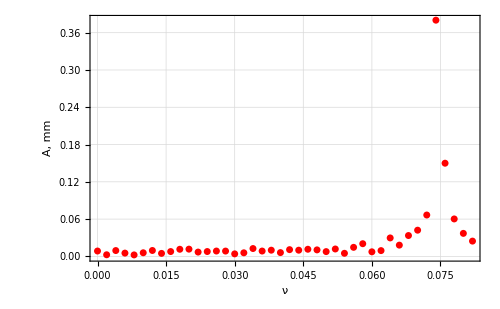

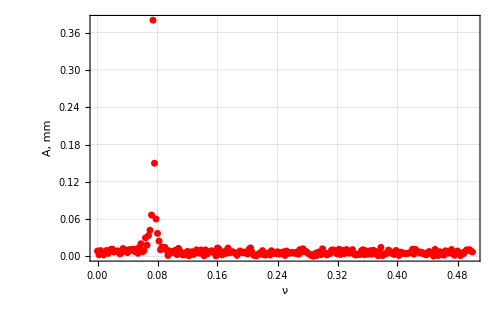

```mathematica
Freq25=Freq[sig25]
NuGass25=NuGass[sig25]
Image25=ListLinePlot[sig25]
Fourier25=TruePlot[sig25]
FourierFull25=FullPlot[sig25]
```

50% Level

0.074

0.0741947

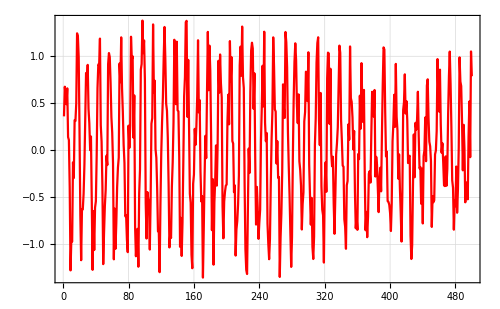

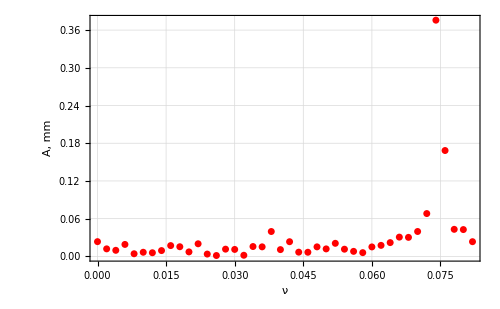

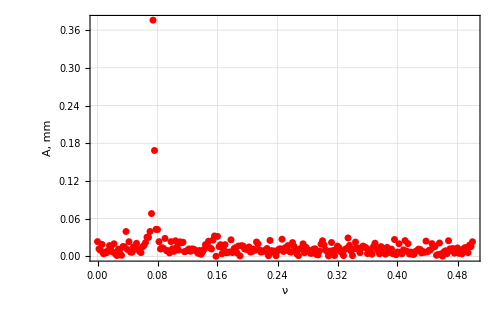

```mathematica
sig50=Table[(Random[]-0.5)+a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,500}];
Freq50 =Freq[sig50]
NuGass50=NuGass[sig50]
Image50=ListLinePlot[sig50]
Fourier50=TruePlot[sig50]
FourierFull50=FullPlot[sig50]
```

75% Level

0.074

0.0740939

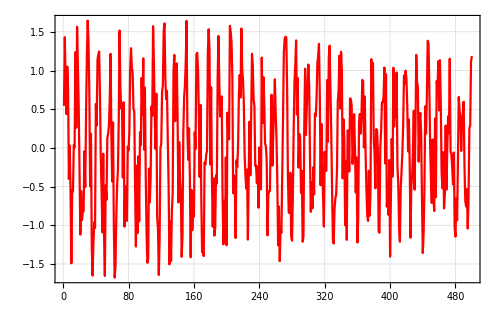

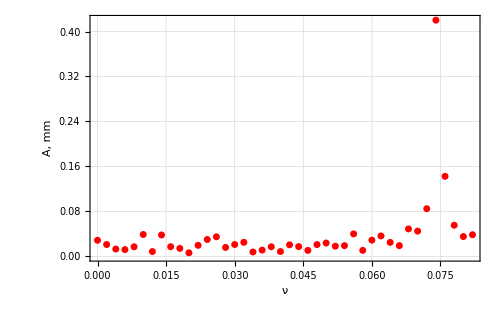

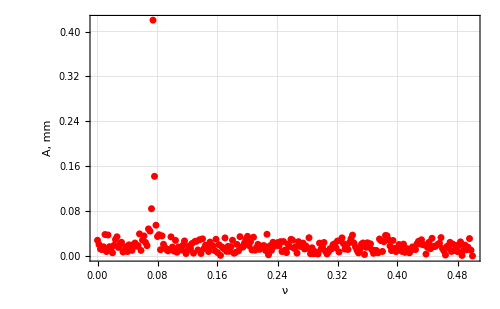

```mathematica
sig75=Table[1.5*(Random[]-0.5)+a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,500}];
Freq75 =Freq[sig75]
NuGass75=NuGass[sig75]
Image75=ListLinePlot[sig75]
Fourier75=TruePlot[sig75]
FourierFull75=FullPlot[sig75]
```

100% Level

0.074

0.0741394

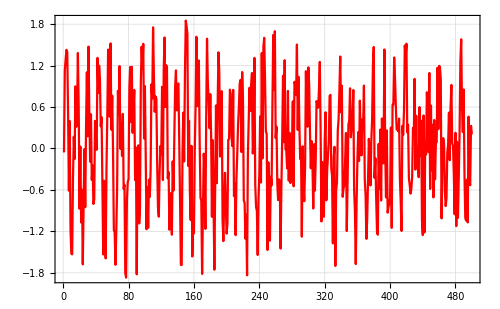

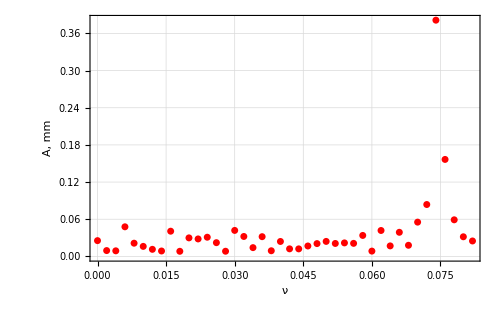

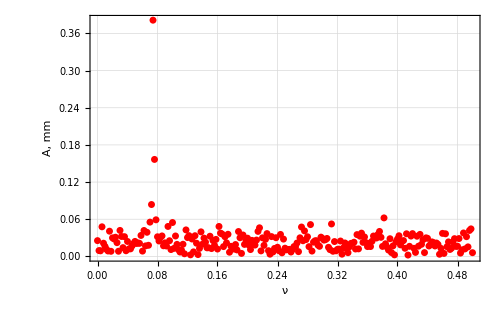

```mathematica
sig100=Table[2*(Random[]-0.5)+a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,500}];
Freq100 =Freq[sig100]
NuGass100=NuGass[sig100]
Image100=ListLinePlot[sig100]
Fourier100=TruePlot[sig100]
FourierFull100=FullPlot[sig100]
```

```mathematica
depen =Transpose[{{0,25,50,75,100},{NuGass0, NuGass25,NuGass50,NuGass75,NuGass100}*10^5-ν*10^5}/.numbers]
```

{{0,-39.2796},{25,-37.6684},{50,-33.5265},{75,-43.6066},{100,-39.0643}}

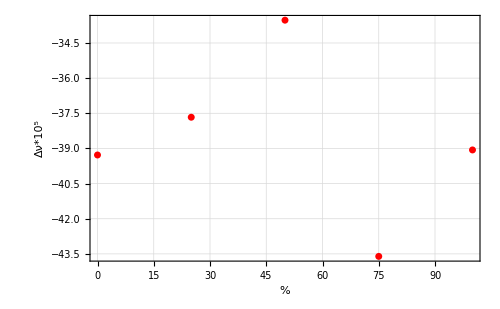

```mathematica
DeltaGass=ListPlot[depen,Axes->True,FrameLabel->{"%","Δν*10^5"}]
```

```mathematica
Export["DeltaGassNoise.png",DeltaGass]
```

DeltaGassNoise.png